```mathematica
point=Table[Zeta[1+t*I],{t,-10,10}]
```

{Zeta[1-10 ⅈ],Zeta[1-9 ⅈ],Zeta[1-8 ⅈ],Zeta[1-7 ⅈ],Zeta[1-6 ⅈ],Zeta[1-5 ⅈ],Zeta[1-4 ⅈ],Zeta[1-3 ⅈ],Zeta[1-2 ⅈ],Zeta[1-ⅈ],ComplexInfinity,Zeta[1+ⅈ],Zeta[1+2 ⅈ],Zeta[1+3 ⅈ],Zeta[1+4 ⅈ],Zeta[1+5 ⅈ],Zeta[1+6 ⅈ],Zeta[1+7 ⅈ],Zeta[1+8 ⅈ],Zeta[1+9 ⅈ],Zeta[1+10 ⅈ]}

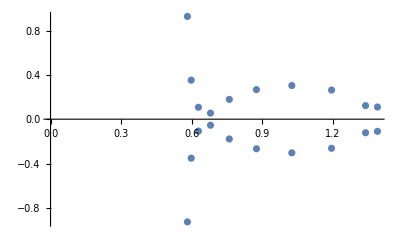

```mathematica
ListPlot[Transpose[{Re[point],Im[point]}],AxesOrigin->{0,0}]
```